# Sink or Swim: Visualizing the effect of sea level rise on a topographical map

Arian Patel

Mentor: Lauren Cooper

## Introduction

As the planet warms, ice melts and oceans expand, resulting in sea level rise. This process threatens many coastal cities, and locations such as Kent Island in Maryland and the Maldives in the Pacific ocean are already considering relocation. In addition to simply flooding areas, sea level rise encourages more extreme weather and poses a major threat to the 40% of the global population that lives close to the sea [1]. 

This project builds off of a previous demonstration to model sea level rise in any location on earth in a more user-friendly manner. The user can view any region and manipulate the sea level; additionally, political boundaries have been added to better visualize the loss of land. Users can also input an address, and a map with multiple zoom levels will be displayed around this address. Finally, an option showing the world if all ice melted has been added.

## Exploring sea level rise

I am using the built in function “GeoElevationData”, which pulls data from a location that can be displayed as 3D graphics or list point plots, and relief plots. The following code displays some examples with the U.S. State of Maryland.

```mathematica
dataMD = GeoElevationData[Entity["AdministrativeDivision",{"Maryland","UnitedStates"}],GeoRange->Quantity[100,"Kilometers"],GeoProjection->Automatic];
```

```mathematica
ListPlot3D[Reverse[dataMD],PlotRange->{Automatic,Automatic,{0,10000}},MeshFunctions->{#3&},Mesh->30,ImageSize->Medium]
```

-Graphics3D-

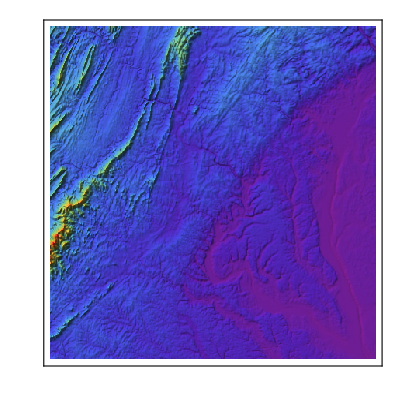

```mathematica
ReliefPlot[Reverse[dataMD],ColorFunction->"Rainbow"]
```

I first explored visually analyzing the relief plots by converting them to a gray scale, and thresholding, or increasing the amount of black. This would simulate the lowest points of the graph taking up more area. While this technique can simulate a rising ocean, it also expands other low points such as depressions. The following code is an example of this technique: ***fix wording/meaning***

```mathematica
image=Image[ReliefPlot[Reverse[dataMD],ColorFunction->"GrayTones"]];
```

```mathematica
Manipulate[Threshold[image,percent],{percent,0,1}]
```

I then explored directly analyzing the data to determine which points were “ocean” and which points were pieces of land below sea level, however this proved to be very challenging.

While searching for possible solutions, I found a wolfram demonstration [2] that simulated a rising sea level. This was accomplished by replacing the lowest z values, or heights, with a new sea level defined by the user:

{elev1, level},
elev1 = QuantityMagnitude[GeoElevationData[Entity["Country", countries], GeoZoomLevel -> Automatic]];
	level = Min[elev1];
elev1 /. z_Real /; z < sea -> level

This core function was then turned into a manipulate in this demonstration :

```mathematica
Manipulate[Module[{elev1,level},
elev1=QuantityMagnitude[GeoElevationData[Entity["Country",countries],GeoZoomLevel->Automatic]];
	level=Min[elev1];
ReliefPlot[elev1/.z_Real/;z<sea->level,DataReversed->True,MaxPlotPoints->ControlActive[300,∞],ImageSize->{600,300}]],{{countries,"UnitedStates","countries"},{"World","Russia","UnitedStates"->"United States","Italy","Canada","UnitedKingdom"->"United Kingdom","India"
}, ControlType->PopupMenu },{{sea,0,"sea level (in feet)"},-400,400,Appearance->"Labeled"},SynchronousUpdating->False,SynchronousInitialization->False,Deployed->True, AutorunSequencing->{2}, Deployed->True]
```

## The functions

With this new base code, I could build a function that takes a location and a change in sea level, and returns the resulting relief plot. This core function is displayed below with a manipulate:

```mathematica
seaLevelRiseFunctionBasicV1[location_,sea_]:=

Module[
{elev1,geodata,level},
geodata=GeoElevationData[location,Automatic,"GeoPosition",GeoZoomLevel->Automatic];
elev1=QuantityMagnitude[GeoElevationData[location,GeoZoomLevel->Automatic]];
level=Min[elev1];

ReliefPlot[elev1/.z_Real/;z<sea->level,DataReversed->True,MaxPlotPoints->ControlActive[300,∞],ImageSize->{600,300},DataRange->{MinMax[geodata[[1,All,All,2]]],MinMax[geodata[[1,All,All,1]]]},ColorFunction->"Rainbow"]]
```

```mathematica
seaLevelRiseBasicV1[location_] := Manipulate[seaLevelRiseFunctionBasicV1[location,sea],{{sea,0, "sea level change in feet"},-400,400,5,Appearance->"Labeled"}]
```

```mathematica
seaLevelRiseBasicV1[LinguisticAssistant]
```

I then implemented political boundaries into the manipulate so that one could use to better visualize the land lost. It was challenging to implement the political boundaries, normally a GeoGraphic, into this non-GeoGraphic based relief plot. However, if you specify “GeoPosition” in the data, you can associate the polygon of the border to the coordinates on the map, and display it with an Epilog. The code below shows the same core function, now with political boundaries.

```mathematica
seaLevelRiseFunctionBasicV2[location_,sea_]:=

Module[
{elev1,geodata,level},
geodata=GeoElevationData[location,Automatic,"GeoPosition",GeoZoomLevel->Automatic];
elev1=QuantityMagnitude[GeoElevationData[location,GeoZoomLevel->Automatic]];
level=Min[elev1];

ReliefPlot[elev1/.z_Real/;z<sea->level,DataReversed->True,MaxPlotPoints->ControlActive[300,∞],ImageSize->{600,300},DataRange->{MinMax[geodata[[1,All,All,2]]],MinMax[geodata[[1,All,All,1]]]},ColorFunction->"Rainbow",Epilog->{EdgeForm[{Cyan,Thickness[0.0009]}],FaceForm[{Opacity[0.07,Blue]}],location["Polygon"]}
]]
```

```mathematica
seaLevelRiseBasicV2[location_] := Manipulate[seaLevelRiseFunctionBasicV2[location,sea],{{sea,0, "sea level change in feet"},-400,400,5,Appearance->"Labeled"}]
```

```mathematica
seaLevelRiseBasicV2[Entity["AdministrativeDivision",{"Virginia","UnitedStates"}]]
```

The next functionality that I implemented was the ability to view your address at multiple “zoom levels”. The user needs to input their information, and the program plots the address at different scales, showing the entire country and providence, for example. This functionality was implemented directly into the core function. This is demonstrated below with a bayside hotel in Maryland.

```mathematica
seaLevelRiseFunction[address_,location_,sea_]:=

Module[
{elev1,geodata,level},
geodata=GeoElevationData[location,Automatic,"GeoPosition",GeoZoomLevel->Automatic];
elev1=QuantityMagnitude[GeoElevationData[location,GeoZoomLevel->Automatic]];
level=Min[elev1];

ReliefPlot[elev1/.z_Real/;z<sea->level,DataReversed->True,MaxPlotPoints->ControlActive[300,∞],ImageSize->{600,300},DataRange->{MinMax[geodata[[1,All,All,2]]],MinMax[geodata[[1,All,All,1]]]},ColorFunction->"Rainbow",
Epilog->{{EdgeForm[{Cyan,Thickness[0.0009]}],FaceForm[{Opacity[0.07,Blue]}],location["Polygon"]},{AbsolutePointSize[10],White,Point[address]}}]]
```

```mathematica
seaLevelRiseAddressV1[street_,city_,state_,country_,county_:"No County given"] := 

Manipulate[

Module[
{address},
address = Interpreter["StreetAddress"][ToString[{street,city["Name"],state["Name"]}]];

seaLevelRiseFunction[address,location,sea]],

	{{location,country,"Zoom Level"},{country,state,county,city}, ControlType->PopupMenu },

	{{sea,0,"sea level change (in feet)"},-400,400,5,Appearance->"Labeled"},

SynchronousUpdating->False,SynchronousInitialization->False,Deployed->True, AutorunSequencing->{2}, Deployed->True]
```

```mathematica
seaLevelRiseAddressV1["100 Heron Blvd",Entity["City",{"Cambridge","Maryland","UnitedStates"}],Entity["AdministrativeDivision",{"Maryland","UnitedStates"}],Entity["Country","UnitedStates"],Entity["AdministrativeDivision",{"DorchesterCounty","Maryland","UnitedStates"}]]
```

This function can take street names either as strings or as plain input, and the rest of the arguments are best taken with natural language input. The counties, or secondary administrative divisions is an optional variable at the end of the function. If no county is given, nothing will display for that zoom level, but the rest of the code is still completely functional.

The final functionality implemented was a shortcut to see a region if all the ice on earth melted. National Geographic predicts that if all ice on earth melted, the combined melted water and thermal expansion would result in 216 feet of sea level rise [3]. Therefore, I have implemented into the manipulate a menu that can display a region at 216 feet of sea level rise, as shown below.

```mathematica
seaLevelRiseAddressV2[street_,city_,state_,country_,county_:"No County given"] := 

Manipulate[

Module[
{address},
address = Interpreter["StreetAddress"][ToString[{street,city["Name"],state["Name"]}]];

seaLevelRiseFunction[address,location,sea]],

	{{location,country,"Zoom Level"},{country,state,county,city}, ControlType->PopupMenu },

	{{sea,0,"sea level change (in feet)"},-400,400,5,Appearance->"Labeled"},

	{sea,{216->"what if all ice melted..."}},

SynchronousUpdating->False,SynchronousInitialization->False,Deployed->True, AutorunSequencing->{2}, Deployed->True]
```

```mathematica
seaLevelRiseAddressV2["9 Cardinal Park dr SE",Entity["City",{"Leesburg","Virginia","UnitedStates"}],LinguisticAssistant,Entity["Country","UnitedStates"],Entity["AdministrativeDivision",{"LoudounCounty","Virginia","UnitedStates"}]]
```

## Conclusions and future work

These plots and GIFs demonstrate that even a small change in sea level can wipe out a large amount of land, such as the states of Florida and Maryland. Additionally, the predicted maximum rise of 216 feet could have strong effects in various regions of the world and has the potential to wipe out many cities and locations without proper preparation for sea level rise. 

In order to make this function more accessible, the functions could be put on a website to allow for anyone to explore sea level rise. This was attempted, but difficulties with Wolfram Cloud arose that will need to be revisited. Another possible feature to revisit would be to return the land lost for any given area, to give more perspective on how a small global change could potentially have a large impact. This could possibly be done by analyzing the amount of ocean or purple pixels in the relief plot, or by analyzing the data directly to select the z-coordinates now at sea level. Finally, the function could consider land that is currently under sea level, such as the Netherlands, more accurately portray how they are filled. Different techniques of elevation data analysis and image processing were explored to address this issue, but the techniques would need to be improved to recognize geological depressions from oceans and to generate proper topological maps in an efficient manner.

#### Citations

[1] https : // sedac.ciesin.columbia.edu/es/papers/Coastal_Zone _Pop _Method.pdf
[2] https : // demonstrations.wolfram.com/SeaLevelRise/
[3] https://www.nationalgeographic.com/magazine/2013/09/rising-seas-ice-melt-new-shoreline-maps/